# LL

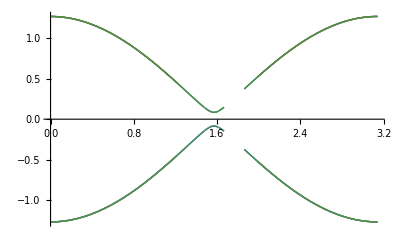

```mathematica
Clear["Global`*"]

σ0=PauliMatrix[0];σx=PauliMatrix[1];σy=PauliMatrix[2];σz=PauliMatrix[3];
v0=PauliMatrix[0];vx=PauliMatrix[1];vy=PauliMatrix[2];vz=PauliMatrix[3];
τ0=PauliMatrix[0];τx=PauliMatrix[1];τy=PauliMatrix[2];τz=PauliMatrix[3];

λ0=0;
t=-0.6;
tp=-0.15;
txy=0.13;
tzo=-0.3;
td=0.03;
tdp=0.1;
t1po=0.3;
t2po=0.06;
tdo=0.06;

kx=-π/2;ky=π/2;

λ=λ0+txy Cos[kx] Cos[ky];
Ep=(2 t-ⅈ tp)(Cos[kx]+Cos[ky]);

ReEp=(2 t)(Cos[kx]+Cos[ky]);
ImEp=(-ⅈ tp)(Cos[kx]+Cos[ky]);

Ez=2 t Cos[kz];
Ezo=(1-ⅈ)tzo Cos[kz];
ReEzo=+tzo Cos[kz];
ImEzo=-tzo Cos[kz];

Ed=td (Cos[kx]+Cos[ky])Cos[kz]+ⅈ tdp (Sin[kx]+Sin[ky])Sin[kz];
ReEd=td   (Cos[kx]+Cos[ky])Cos[kz];
ImEd=tdp (Sin[kx]+Sin[ky])Sin[kz];

Epo=t1po Cos[kx]+t2po Cos[ky]-ⅈ(t2po Cos[kx]+t1po Cos[ky]);
ReEpo=+(t1po Cos[kx]+t2po Cos[ky]);
ImEpo=-(t2po Cos[kx]+t1po Cos[ky]);

Edo=tdo(Sin[ky]+ⅈ Sin[kx])Sin[kz];
ReEdo=tdo(Sin[ky])Sin[kz];
ImEdo=tdo(Sin[kx])Sin[kz];


H=λ KroneckerProduct[σ0,KroneckerProduct[v0,τ0]]+ReEp KroneckerProduct[σ0,KroneckerProduct[v0,τx]]+ImEp KroneckerProduct[σz,KroneckerProduct[v0,τy]]+Ez KroneckerProduct[σ0,KroneckerProduct[vx,τ0]]+ReEd KroneckerProduct[σ0,KroneckerProduct[vx,τx]]+ImEd KroneckerProduct[σ0,KroneckerProduct[vy,τy]]+ReEpo KroneckerProduct[σy,KroneckerProduct[vz,τy]]+ImEpo KroneckerProduct[σx,KroneckerProduct[vz,τy]]+ReEzo KroneckerProduct[σy,KroneckerProduct[vy,τz]]+ImEzo KroneckerProduct[σx,KroneckerProduct[vy,τz]]+ReEdo KroneckerProduct[σy,KroneckerProduct[vy,τx]]+ImEdo KroneckerProduct[σx,KroneckerProduct[vy,τx]];


eig=Eigenvalues[H];
Plot[eig,{kz,0,π}]
```